```mathematica
(*with rfd, 5000 non interacting particles*)
SetDirectory[NotebookDirectory[]];
dir="/home/drladiges/gigan/projects/FHDeX/exec/";
file="ascii_means000245000";
count=8;
slist={"A","B","C","D","E","F","G","H"};
rawList=Table[0,{ii,1,count}];
(*dir="/home/drladiges/projects/FHDeX/exec/";.
file="ascii_means000000150";*)

For[kk=1,kk≤8,kk++,
raw0=Import[dir<>"immersedIons"<>slist[[kk]]<>"/0_"<>file,"Table"];
raw1=Import[dir<>"immersedIons"<>slist[[kk]]<>"/1_"<>file,"Table"];
raw2=Import[dir<>"immersedIons"<>slist[[kk]]<>"/2_"<>file,"Table"];
raw3=Import[dir<>"immersedIons"<>slist[[kk]]<>"/3_"<>file,"Table"];
rawA=Join[raw0[[1;;-3]],raw1[[1;;-3]],raw2[[1;;-3]],raw3[[1;;-3]]];
rawList[[kk]]=rawA;
];
```

```mathematica
(*xsize=64;
ysize=64;
zsize=32;*)
xsize=128;
ysize=128;
zsize=64;
cell=1;

func3D=Table[0,{ii,1,count}];
func2D=Table[0,{ii,1,count}];

For[ll=1,ll≤8,ll++,
members3DA=Table[{ToExpression[StringReplace[rawList[[ll,ii,1]],{"("-> "{",")"-> "}"}]],rawList[[ll,ii,3]]},{ii,1,Length[rawList[[ll]]]}];
func3D[[ll]]=Interpolation[members3DA,InterpolationOrder->1];
membersFlat=Flatten[Table[{{ii,jj},Mean[Table[func3D[[ll]][ii,jj,kk],{kk,0,zsize-1,cell}]]},{ii,0,xsize-1},{jj,0,ysize-1}],1];
func2D[[ll]]=Interpolation[membersFlat,InterpolationOrder->1];
];

(*members3DB=Table[{ToExpression[StringReplace[rawB[[ii,1]],{"("-> "{",")"-> "}"}]],rawB[[ii,3]]},{ii,1,Length[rawB]}];
func3DB=Interpolation[members3DB,InterpolationOrder->1];
membersFlat=Flatten[Table[{{ii,jj},Mean[Table[func3DB[ii,jj,kk],{kk,0,zsize-1,cell}]]},{ii,0,xsize-1},{jj,0,ysize-1}],1];
func2DB=Interpolation[membersFlat,InterpolationOrder->1];

members3DC=Table[{ToExpression[StringReplace[rawC[[ii,1]],{"("-> "{",")"-> "}"}]],rawC[[ii,3]]},{ii,1,Length[rawC]}];
func3DC=Interpolation[members3DC,InterpolationOrder->1];
membersFlat=Flatten[Table[{{ii,jj},Mean[Table[func3DC[ii,jj,kk],{kk,0,zsize-1,cell}]]},{ii,0,xsize-1},{jj,0,ysize-1}],1];
func2DC=Interpolation[membersFlat,InterpolationOrder->1];

members3DD=Table[{ToExpression[StringReplace[rawD[[ii,1]],{"("-> "{",")"-> "}"}]],rawD[[ii,3]]},{ii,1,Length[rawD]}];
func3DD=Interpolation[members3DD,InterpolationOrder->1];
membersFlat=Flatten[Table[{{ii,jj},Mean[Table[func3DD[ii,jj,kk],{kk,0,zsize-1,cell}]]},{ii,0,xsize-1},{jj,0,ysize-1}],1];
func2DD=Interpolation[membersFlat,InterpolationOrder->1];*)
```

```mathematica
func2DM[x_,y_] = Sum[func2D[[ll]][x,y],{ll,1,count}]/count;
DensityPlot[func2DM[x,y],{x,0,xsize-1},{y,0,ysize-1},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->256]
```

-Graphics-

```mathematica
membersFlatter=Flatten[Table[{{jj,Mean[Table[func2DM[ii,jj],{ii,0,xsize-1,cell}]]}},{jj,0,ysize-1}],1];
func1DM=Interpolation[membersFlatter,InterpolationOrder->1];
```

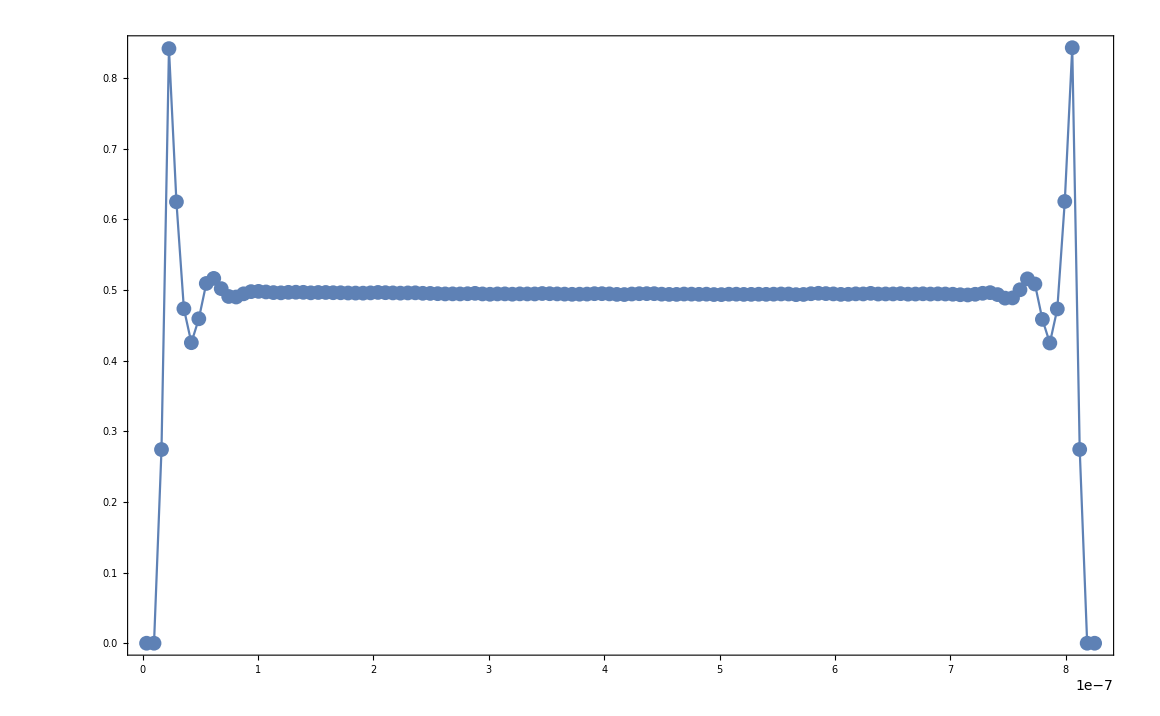

```mathematica
pa=ListPlot[Table[{y,func1DM[posFunc[y]]},{y,dx/2,size-dx/2,dx}]];
pb=Plot[func1DM[posFunc[y]],{y,dx/2,size-dx/2},PlotRange->All];
Show[pa,pb,PlotRange->All,Frame->True,Axes->False]
```

```mathematica
size=8.284925963482451*10^-7;
dx=size/128;
posFunc[x_]=x/dx -0.5;
```

127.

```mathematica
2*3424*(4/3 π (0.2*10^-7)^3)/(size^2*(size/2))
```

0.807061

```mathematica
func2D[[1]][5,5]
```

0.478488